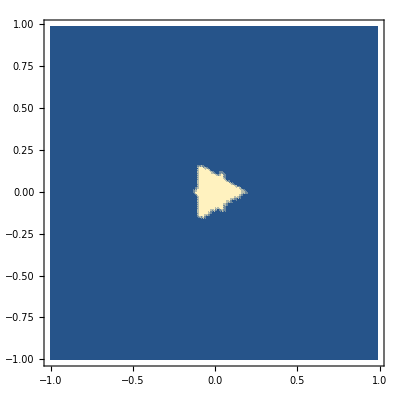

```mathematica
(*Model Parameters*)
θb=60 2Pi/360;  (*angle between paired legs on the bottom*)
rb=1;                            (*radius of bottom*)

θt=20 2Pi/360;   (*leg angle on top*)
rt=1/2;                      (*radius of top*);

h = 1; (*equilibrium height of the platform. No tilt, all legs 0 displacemnt. The eqilibrium length is calculated based on this height*)
l = .2; (*radius of servo horn*)

(*test parameters*)
ϕRange = 35 Degree; (*desired maximum tilt angle in worst case direction for any position*);
lRange = 1;                  (*linear range to test. x= -lRange to +lRange, y = -lRange to +lRange*);



ϕb=(2 Pi-3θb)/3; 
ϕt=(2 Pi-3θt)/3;
ϵ=1/100;
ptsb=Table[rb{Cos[ang-θb/2],Sin[ang-θb/2]},{ang,0,2π-ϵ,θb+ϕb}]~Riffle~Table[rb{Cos[ang-θb/2],Sin[ang-θb/2]},{ang,θb,2π+θb-ϵ,θb+ϕb}];
ptsb=#~Join~{0,1}&/@ptsb;
ptsb=Transpose[ptsb];
ptst=Table[rt{Cos[ang-θt/2],Sin[ang-θt/2]},{ang,0,2π-ϵ,θt+ϕt}]~Riffle~Table[rt{Cos[ang-θt/2],Sin[ang-θt/2]},{ang,θt,2π+θt-ϵ,θt+ϕt}];
ptst=#~Join~{0,1}&/@ptst;
ptst=Transpose[ptst];
rotMat[α_,β_,γ_]:=(#~Join~{0}&/@RollPitchYawMatrix[{α,β,γ}])~Join~{{0,0,0,1}};

i = {1,0,0};
j = {0,1,0};
k = {0,0,1};
norm[x_]:=Sqrt[x.x];
unit[x_]:=x/norm[x];
normMat[u_,θ_]:=With[{l=j*Cos[θ]+i*Sin[θ]},Transpose[{unit[l~Cross~u] ~Join~{0},unit[u~Cross~unit[l~Cross~u]]~Join~{0},unit[u]~Join~{0},{0,0,0,1}}]]
normMat[u_] := normMat[u,0];
normMat[a_,b_,c_,θ_]:=normMat[{a,b,c},θ];
normMat[a_,b_,c_]:=normMat[{a,b,c},0];

tMat[x_,y_,z_]:={{1,0,0,x},{0,1,0,y},{0,0,1,z},{0,0,0,1}};
top[x_,y_,θ_,ϕ_]:=tMat[x,y,h].normMat[Sin[ϕ]Cos[θ],Sin[ϕ]Sin[θ],Cos[ϕ]].ptst;
dists[x_,y_,θ_,ϕ_]:=norm/@Transpose[top[x,y,θ,ϕ]-ptsb]//N;
modelB[b_] := Transpose[b[[1;;-2]]]~Join~{Transpose[b[[1;;-2]]][[1]]} ;
riffle[x_,y_]:=Fold[Join,Table[{y[[2i-1]],x[[2i-1]],x[[2i]],y[[2i]]},{i,1,Length[x]/2}]]
modelC[b_,t_]:=riffle[Transpose[b[[1;;-2]]],Transpose[t[[1;;-2]]]];
model[b_,t_]:={Line[modelB[b]],Line[modelB[t]],Line[modelC[b,t]]};

d0 =dists[0,0,0,0][[1]];
ln=150;
atan[x_,y_]:=If[x==0&&y==0,0,ArcTan[x,y]];
Manipulate[Graphics3D[model[ptsb,top[x,y,atan[x,y],ϕRange]]],{x,-lRange,lRange},{y,-lRange,lRange}]

distsWithinSpec[x_,y_,θ_,ϕ_]:=AllTrue[Map[Abs[#-d0]<l&,dists[x,y,θ,ϕ]],#&];

t=Table[{x,y,atan[x,y],ϕRange},{x,-lRange,lRange,2 lRange/ln},{y,-lRange,lRange,2 lRange/ln}]//N;
works=Map[distsWithinSpec@@#&,t,{2}];
xAxis = Table[x,{x,-lRange,lRange,2lRange/ln}];
yAxis = xAxis;
list = Table[{xAxis[[x]],yAxis[[y]],If[works[[x,y]],1,0]},{x,1,ln},{y,1,ln}];
list=Flatten[list,1];
ListDensityPlot[list]
(*Yellow means possible, blue means impossible*)
(*also shows what the patform looks like in the worst case for each position*)
```